```mathematica
Factor[CharacteristicPolynomial[ConversionMatrix["E","C"],x]]
```

(-1+x)^52

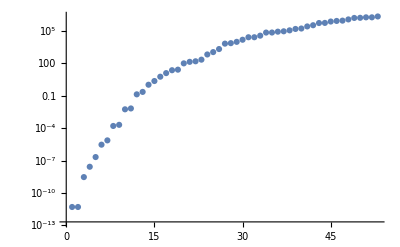

```mathematica
CoefficientList[CharacteristicPolynomial[ConversionMatrix["C","F"],x],x]//Abs//Sort//ListLogPlot
```

```mathematica
CoefficientList[(1+3 x-15 x^2-14 x^3+28 x^4+24 x^5),x]
```

{1,3,-15,-14,28,24}

```mathematica
Length[allGraphs6]
```

0

```mathematica
{1,3,-15,-14,28,24}
```

{1,3,-15,-14,28,24}

```mathematica
576
```

576

```mathematica
FactorInteger[576]
```

{{2,6},{3,2}}

```mathematica
Keys[Bases6]
```

{C,E,G,F}

```mathematica
]
```

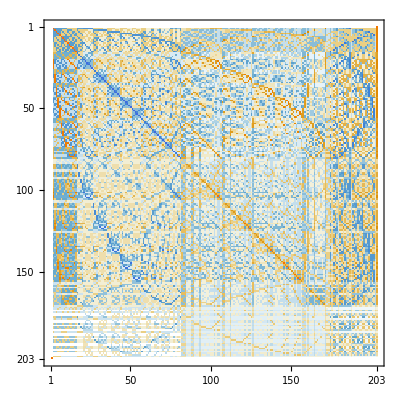

```mathematica
ConversionMatrix6["G","F"]//MatrixPlot
```

```mathematica
Table[ Factor[CharacteristicPolynomial[ConversionMatrix6[base1,base2],x]],{base1,Keys[Bases6]},{base2,Keys[Bases6]}]//TableForm
```

-(-1+x)^203 | -(-1+x)^203 | -(-1+x)^203 | -((1+2 x)^10 (-1+3 x+x^2)^5 (-1+2 x+2 x^2)^16 (-1+6 x+4 x^2)^5 (1+9 x-128 x^2-186 x^3+2164 x^4+1776 x^5-7248 x^6-3168 x^7+6912 x^8)^5 (-1-10 x+176 x^2+55 x^3-3314 x^4-742 x^5+16812 x^6+10000 x^7-11760 x^8-6432 x^9+1152 x^10)^9 (1-79 x-1344 x^2+15450 x^3+36598 x^4-390326 x^5-325988 x^6+2319000 x^7+830688 x^8-4292352 x^9-317952 x^10+1658880 x^11))/6426666657455535625651051273371558183683294526786393206811525120
-(-1+x)^203 | -(-1+x)^203 | -(-1+x)^11 (1+x+x^2)^26 (1-6 x+4 x^2+31 x^3+12 x^4+31 x^5+4 x^6-6 x^7+x^8)^5 (1-x-x^2-7 x^3+23 x^4-22 x^5+23 x^6-7 x^7-x^8-x^9+x^10)^9 (1+23 x+286 x^2+2458 x^3+10538 x^4+19600 x^5+10538 x^6+2458 x^7+286 x^8+23 x^9+x^10) | -((-1+x)^46 (1+x)^30 (-1+2 x)^20 (1+2 x)^60 (-1+4 x)^10 (-1+6 x)^15 (1+6 x)^15 (-1+24 x)^6 (1+120 x))/6426666657455535625651051273371558183683294526786393206811525120
-(-1+x)^203 | -(-1+x)^11 (1+x+x^2)^26 (1-6 x+4 x^2+31 x^3+12 x^4+31 x^5+4 x^6-6 x^7+x^8)^5 (1-x-x^2-7 x^3+23 x^4-22 x^5+23 x^6-7 x^7-x^8-x^9+x^10)^9 (1+23 x+286 x^2+2458 x^3+10538 x^4+19600 x^5+10538 x^6+2458 x^7+286 x^8+23 x^9+x^10) | -(-1+x)^203 | -((-1+x)^46 (1+x)^30 (-1+2 x)^20 (1+2 x)^60 (-1+4 x)^10 (-1+6 x)^15 (1+6 x)^15 (-1+24 x)^6 (1+120 x))/6426666657455535625651051273371558183683294526786393206811525120
-(2+x)^10 (-4-6 x+x^2)^5 (-1-3 x+x^2)^5 (-2-2 x+x^2)^16 (6912-3168 x-7248 x^2+1776 x^3+2164 x^4-186 x^5-128 x^6+9 x^7+x^8)^5 (-1152+6432 x+11760 x^2-10000 x^3-16812 x^4+742 x^5+3314 x^6-55 x^7-176 x^8+10 x^9+x^10)^9 (1658880-317952 x-4292352 x^2+830688 x^3+2319000 x^4-325988 x^5-390326 x^6+36598 x^7+15450 x^8-1344 x^9-79 x^10+x^11) | -(-24+x)^6 (-6+x)^15 (-4+x)^10 (-2+x)^20 (-1+x)^46 (1+x)^30 (2+x)^60 (6+x)^15 (120+x) | -(-24+x)^6 (-6+x)^15 (-4+x)^10 (-2+x)^20 (-1+x)^46 (1+x)^30 (2+x)^60 (6+x)^15 (120+x) | -(-1+x)^203

```mathematica
Factor[CharacteristicPolynomial[Factor[CharacteristicPolynomial[ConversionMatrix6["E","F"],x]],x]]
```

-x^203

```mathematica
FactorInteger[195689447424]
```

{{2,28},{3,6}}

```mathematica
allGraphs5[alfa1Key,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240

```mathematica
ShowGenerator[k_]:=allGraphs5[k,"graph"]->(allGraphs5[k,"colofourgenerator"]/.RepGraph["G"])
```

```mathematica
ShowGenerator[alfa1Key]
```

-Graphics-→-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240

```mathematica
Table[ShowGenerator[k],{k,alfa1s}]//TableForm
```

-Graphics-→-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240
-Graphics-→-Graphics-273100--Graphics-294970--Graphics-273370+-Graphics-295240
-Graphics-→-Graphics-294400--Graphics-295210--Graphics-294430+-Graphics-295240
-Graphics-→-Graphics-229360--Graphics-294970--Graphics-229630+-Graphics-295240
-Graphics-→-Graphics-273340--Graphics-295210--Graphics-273370+-Graphics-295240

```mathematica
allGraphs5[22963,"colofour"]/.RepGraph["C"]
```

-Graphics-360850+-Graphics-295240

```mathematica
allGraphs5[29443,"colofour"]/.RepGraph["C"]
```

-Graphics-296050+-Graphics-295240

```mathematica
allGraphs5[22882,"colofour"]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-360850+-Graphics-296050+-Graphics-295240

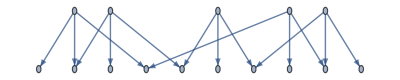

```mathematica
Graph[Table[Map[allGraphs5[k,"graph"]->#&,(ListofVars[allGraphs5[k,"colofour"]]/.RepGraph["C"])],{k,alfas}]//Flatten]
```

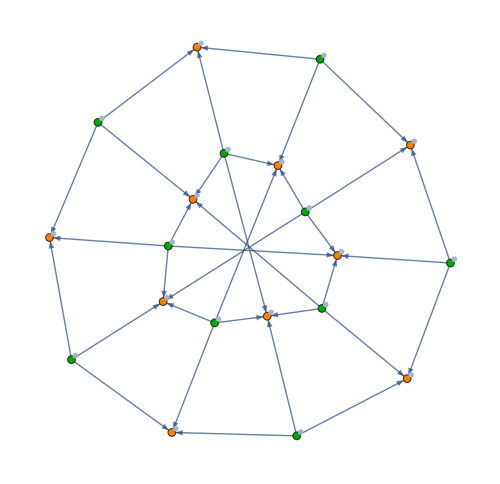

```mathematica
With[{g=VertexDelete[Graph[Flatten[Table[Map[k->#&,(ListofVars[allGraphs5[k,"colofour"]]/.RepKey["C"])],{k,Join[amigos,alfas]}]]],K5Key]},
Graph[g, 
VertexLabels->Map[#->allGraphs5[#,"graph"]&,VertexList[g]],
VertexStyle->Map[#->ColourForKey [allGraphs5,#]&,VertexList[g]],
GraphLayout->"SpringElectricalEmbedding",
ImageSize->500
]]
```

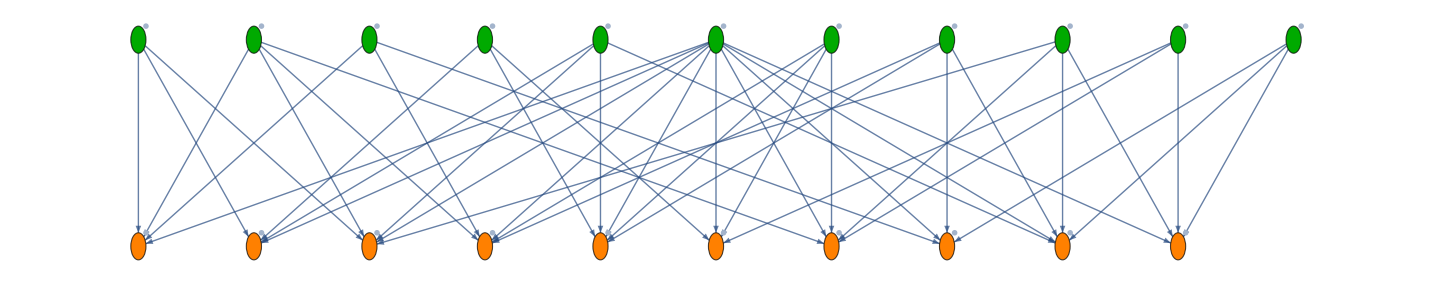

```mathematica
With[{g=VertexDelete[Graph[Flatten[Table[Map[k->#&,(ListofVars[allGraphs5[k,"colofour"]]/.RepKey["C"])],{k,Join[amigos,alfas,{lambdaKey}]}]]],K5Key]},
Graph[g, 
VertexLabels->Map[#->allGraphs5[#,"graph"]&,VertexList[g]],
VertexStyle->Map[#->ColourForKey [allGraphs5,#]&,VertexList[g]],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->500
]]
```

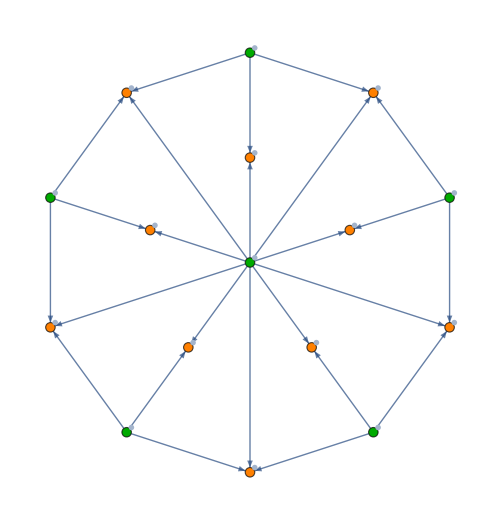

```mathematica
With[{g=VertexDelete[Graph[Flatten[Table[Map[k->#&,(ListofVars[allGraphs5[k,"colofour"]]/.RepKey["C"])],{k,Join[alfas,{lambdaKey}]}]]],K5Key]},
Graph[g, 
VertexLabels->Map[#->allGraphs5[#,"graph"]&,VertexList[g]],
VertexStyle->Map[#->ColourForKey [allGraphs5,#]&,VertexList[g]],
GraphLayout->"TutteEmbedding",
ImageSize->500
]]
```

```mathematica
With[{g=VertexDelete[Graph[Flatten[Table[Map[k->#&,(ListofVars[allGraphs5[k,"colofour"]]/.RepKey["C"])],{k,Join[amigos]}]]],K5Key]},
Graph[g, 
VertexLabels->Map[#->allGraphs5[#,"graph"]&,VertexList[g]],
VertexStyle->Map[#->ColourForKey [allGraphs5,#]&,VertexList[g]],
GraphLayout->"TutteEmbedding",
ImageSize->500
]]
```